```mathematica
DFT[k_,X_]:={k/Length[X],Total[X*Table[Exp[-2 Pi I k ind/Length[X] ],{ind,0,Length[X]-1}]]/Length[X]}
```

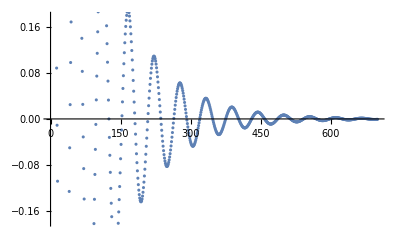

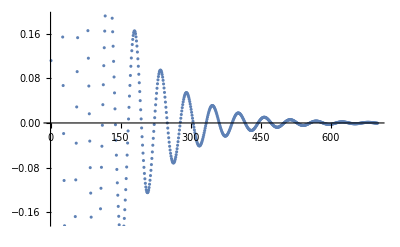

```mathematica
l1 = Table[Exp[I 2 Pi x*0.018-x/100],{x,700}];
ListPlot[Re[l1]]
ListPlot[Im[l1]]
```

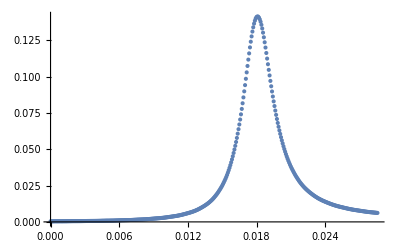

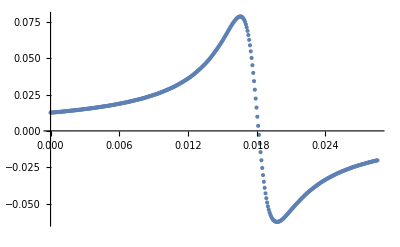

```mathematica
ListPlot[(Table[DFT[i,l1],{i,0,20,0.05}]//N)/.{x_,y_}:>{x,y//Re},PlotRange->All]
ListPlot[(Table[DFT[i,l1],{i,0,20,0.05}]//N)/.{x_,y_}:>{x,y//Im},PlotRange->All]
```

```mathematica
DFT2D[k1_,k2_,X_]:={
{k1/Length[X[[1]]],k2/Length[Transpose[X][[1]]]},Total[X*Table[{Exp[-2 Pi I (k1 ind1 + k2 ind2)/Length[X] ]},
{ind1,0,Length[X]-1},{ind2,0,Length[X]-1}],2]/Length[X]}
```

```mathematica
VDFT2D[k1_,k2_,X_]:=(Total[X*Table[{Exp[-2 Pi I (k1 ind1 + k2 ind2)/Length[X] ]},
{ind1,0,Length[X]-1},{ind2,0,Length[X]-1}],2]/Length[X])[[1]]
```

```mathematica
l2d=Table[Cos[0.1 *2 Pi i+0.2*2Pi j],{i,0,30},{j,0,30}];
```

```mathematica
ListPlot3D[l2d,InterpolationOrder->0,Mesh->None,Filling->Axis]
```

-Graphics3D-

```mathematica
ListPlot3D[Abs[Table[VDFT2D[i,j,l2d],{i,0,30},{j,0,30}]],InterpolationOrder->0,Mesh->None,Filling->Axis,PlotRange->All]
```

-Graphics3D-